# An analysis of SARS - CoV2 Data and Forecasts

## Introduction

We are analyzing the existing  available data on daily deaths caused by the SARS-CoV2 virus and use that in conjunction with certain simple models to predict the evolution of the disease in certain geographical areas.

### Selected Data

While we have a lot of data available, including numbers of confirmed cases, numbers of recoveries and numbers of deaths, we are only going to use the number of deaths. One reason for this is that the number of confirmed cases is highly dependent on the testing policies for each geographical area and they have no uniform predictive power over the outcomes of the disease progression. We also are not using the number of confirmed recoveries, because each recovery is tied to a confirmed case, and hence we would expose ourselves to the same discretionary policies. We are going to confine our analysis solely to the confirmed deaths data, as that is much more immune to various testing policies.

### Geographical regions

We are going to cover for the purpose of this entry only data from certain regions in Europe and North America, as for these regions it is less likely for deaths to be misreported, or to be counterfeited by various governments. So for now, the analysis is done on the following regions in North America: Washington, California, Colorado, New York, New Jersey, Florida, Michigan, Louisiana, Illinois, Georgia, Massachusetts, Texas, Indiana, Maryland, Pennsylvania, Wisconsin, Nevada, Kentucky, Ohio, Connecticut, Virginia, and North Carolina. Also, it is done on the following regions in Europe: Italy, Spain, Germany, Netherlands, France, Switzerland, Belgium, Romania, Sweden, Greece, United Kingdom, Ireland, Portugal and Austria. Few more regions will be added in the next few days.

### Model

During the initial stages of an outbreak, the growth in casualties grows exponentially. For this period we are using a simple exponential function:

F(t)=c/((1+ⅇ^(b(a-x)))^α)

This is a very universal formula that captures the evolution of any kind of outbreak that occurs in the natural world. As we will show here below, it also captures well the Spanish Flu outbreak from 1918 in New York City. It is very universal, since it has a flexible start time, captured by parameter a, it has a flexible slope and size and it also allows for uneven progression on the way up and down. Some of the useful parameters extracted from this fit are:

median time=a-Log[2^(1/α)-1]/b

size=c (the total number of people who would die)

speed=b*α (the exponential rate during the onset of the outbreak)

skewness=α (the ratio between the exponential rate during the rise of the outbreak and the dieoff)

## The code for loading the data and applying the fit

Loading the data from the file and separating the headers (the files are attached here too).

```mathematica
ts=Import["~/Data/SARSnow.csv"];
regions=ts⟦1⟧//Rest;
date=ts//Rest;
```

Defining a function that changes a daily number to a cumulative death number array, associated to its corresponding day.

```mathematica
tofit[ux_]:=Select[Transpose[{(Transpose@date)⟦1⟧,Accumulate[(date//Transpose)⟦1+Position[regions,ux]⟦1⟧⟦1⟧⟧]}],#⟦2⟧>4&]
```

Defining an association that correlates the letter codes from the file to geographical objects in Mathematica:

```mathematica
sf=<|"Population"->5500000,"Name"->"NYC Spanish flu"|>;
nowregions=<|"WA"->Interpreter["USState"]["Washington"],"CA"->Interpreter["USState"]["California"],"NJ"->Interpreter["USState"]["New Jersey"],"CO"->Interpreter["USState"]["Colorado"],"NY"->Interpreter["USState"]["New York"],"FR"->Interpreter["Country"]["France"],"IT"->Interpreter["Country"]["Italy"],"NL"->Interpreter["Country"]["Netherlands"],"SP"->Interpreter["Country"]["Spain"],"DE"->Interpreter["Country"]["Germany"],"FL"->Interpreter["USState"]["Florida"],"MI"->Interpreter["USState"]["Michigan"],"LA"->Interpreter["USState"]["Louisiana"],"IL"->Interpreter["USState"]["Illinois"],"GA"->Interpreter["USState"]["Georgia"],"MA"->Interpreter["USState"]["Massachusetts"],"TX"->Interpreter["USState"]["Texas"],"IN"->Interpreter["USState"]["Indiana"],"MD"->Interpreter["USState"]["Maryland"],"PA"->Interpreter["USState"]["Pennsylvania"],"WI"->Interpreter["USState"]["Wisconsin"],"CH"->Interpreter["Country"]["Switzerland"],"BE"->Interpreter["Country"]["Belgium"],"RO"->Interpreter["Country"]["Romania"],"SW"->Interpreter["Country"]["Sweden"],"NV"->Interpreter["USState"]["Nevada"],"GR"->Interpreter["Country"]["Greece"],"SF"->sf,"KY"->Interpreter["USState"]["Kentucky"],"UK"->Interpreter["Country"]["United Kingdom"],"OH"->Interpreter["USState"]["Ohio"],"IR"->Interpreter["Country"]["Ireland"],"CT"->Interpreter["USState"]["Connecticut"],"PT"->Interpreter["Country"]["Portugal"],"VA"->Interpreter["USState"]["Virginia"],"AT"->Interpreter["Country"]["Austria"],"NC"->Interpreter["USState"]["North Carolina"]|>;
```

Assigning the ICAO code to the most representative airport from each region. This is used only in the last section when we try to capture weather data from the airport weather stations.

```mathematica
airports=<|"WA"->"KBFI","CA"->"KLAX","NJ"->"KEWR","CO"->"KDEN","NY"->"KLGA","FR"->"LFPO","IT"->"LIML","NL"->"EHAM","SP"->"LEMD","DE"->"EDDF","FL"->"KMIA","MI"->"KDTW","LA"->"KMSY","IL"->"KMDW","GA"->"KATL","MA"->"KBOS","TX"->"KDFW","IN"->"KIND","MD"->"KBWI","PA"->"KPHL","WI"->"KMKE","CH"->"LSZH","BE"->"EBBR","RO"->"LRBC","SW"->"ESSA","NV"->"KLAS","GR"->"LGAV","KY"->"KSDF","UK"->"EGLL","OH"->"KCLE","IR"->"EIDW","CT"->"KBDR","PT"->"LPPT","VA"->"KIAD","AT"->"LOWW","NC"->"KCLT"|>;
```

Defining the function that initialized the model and performs the fit.

```mathematica
functions={};
points={};
model=c/((1+ⅇ^(b(a-x)))^α);
FittedLogit[region_]:=Module[{data=tofit[region]},
modelf=NonlinearModelFit[data,{model,b<10,b>0,a>10,α>0.15},{a,b,c,α},x,Method->"NMinimize",MaxIterations->15000,Weights->(Transpose[data]⟦2⟧)^-0.1];
fit=modelf["BestFitParameters"];
{{region,Values[fit]⟦1⟧-Log[2^(1/Values[fit]⟦4⟧)-1]/(Values[fit]⟦2⟧),Values[fit]⟦2⟧*Values[fit]⟦4⟧,Values[fit]⟦3⟧,Values[fit]⟦4⟧,modelf["AICc"]},modelf,data}
]
```

Launching parallel subkernels to be able to perform the fit in parallel. In some Mathematica this is not necessary, since they are already launched by default.

```mathematica
LaunchKernels[];
```

```mathematica
Off[FittedModel::constr]
```

Performing the fit:

```mathematica
result=Quiet[ParallelMap[FittedLogit,regions]];
```

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

FittedModel::constr: The property values {AICc} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Assigning the fit results to their respective variables:

```mathematica
params=Prepend[Transpose[result]⟦1⟧,{"Region","Median","speed","Size","α","AICc"}];
functions=Transpose[result]⟦2⟧;
points=Transpose[result]⟦3⟧;
```

Probing the asymptotic behavior of the model. This is unrelated to the flow of the code, so it can be skipped. It’s shown here so you can see that the model has the required asymptotic behavior.

```mathematica
g[x_]:=Evaluate@D[c/((1+ⅇ^(b(a-x)))^α),x];
```

```mathematica
h[x_]=Evaluate@D[Log[g[x]],x];
```

(ⅇ^(-b (a-x)) (1+ⅇ^(b (a-x)))^(1+α) (-b^2 c ⅇ^(b (a-x)) (1+ⅇ^(b (a-x)))^(-1-α) α-b^2 c ⅇ^(2 b (a-x)) (1+ⅇ^(b (a-x)))^(-2-α) (-1-α) α))/(b c α)

```mathematica
Limit[h[x],x->∞]
```

ConditionalExpression[-b,(1/c|a|α|c)∈ℝ&&b>0]

Displaying the results of the fit in table form.

```mathematica
Grid[Sort[params,#1⟦6⟧>#2⟦6⟧&],Frame->All]
```

Region | Median | speed | Size | α | AICc
IT | 39.8901 | 0.617484 | 28696.4 | 7.77802 | 792.208
FR | 46.6206 | 0.322358 | 24911.8 | 2.54774 | 671.875
SP | 42.3382 | 1.41897 | 25304.4 | 15.0286 | 655.083
UK | 50.912 | 0.506026 | 24291.7 | 4.73784 | 551.408
SF | 36.8828 | 0.254368 | 11002.2 | 1.75878 | 509.229
DE | 53.9194 | 1.45645 | 8483.83 | 19.3255 | 456.127
NY | 50.4799 | 0.625049 | 20959.1 | 5.64197 | 454.363
NL | 47.657 | 1.35945 | 5206.69 | 16.3169 | 448.245
BE | 49.6787 | 0.236159 | 7594.78 | 1.52865 | 417.074
NJ | 58.4525 | 1.27722 | 9976.48 | 16.1735 | 412.029
SW | 61.6601 | 1.10263 | 4187.09 | 17.6907 | 397.701
WA | 44.6018 | 0.127425 | 820.012 | 1.14075 | 352.074
CA | 70.4832 | 0.66012 | 4670.17 | 13.5478 | 343.215
MI | 54.1911 | 1.25326 | 4405.77 | 14.3442 | 322.993
CH | 45.5684 | 0.650686 | 1830.11 | 6.89982 | 321.294
LA | 53.3457 | 1.46374 | 2302.21 | 19.2054 | 316.398
CT | 66.5592 | 0.635842 | 4765.76 | 9.30341 | 315.462
PA | 97.8528 | 0.736674 | 29100.7 | 19.4992 | 313.263
GA | 58.069 | 0.993732 | 1609. | 15.4882 | 306.792
FL | 56.0261 | 0.566174 | 1583.41 | 6.95392 | 300.407
IL | 59.3331 | 1.44308 | 3151.83 | 19.3917 | 286.409
MA | 65.8029 | 0.41763 | 6589.73 | 5.51978 | 286.279
IN | 53.0459 | 0.355135 | 950.452 | 3.13891 | 256.156
OH | 68.8008 | 0.906154 | 1880.81 | 16.8176 | 253.292
IR | 70.7415 | 0.857585 | 2676.4 | 16.5326 | 241.004
AT | 47.5109 | 1.69537 | 641.018 | 19.2396 | 236.702
PT | 50.8948 | 1.38257 | 1132.85 | 17.5911 | 236.082
TX | 52.7409 | 0.253847 | 822.228 | 2.18589 | 223.84
MD | 54.3898 | 0.193609 | 942.698 | 0.835343 | 221.22
CO | 54.7047 | 1.48859 | 825.159 | 19.9196 | 221.142
RO | 52.3766 | 1.75453 | 766.951 | 21.6927 | 214.964
VA | 66.6906 | 0.178736 | 1121.28 | 2.16659 | 206.827
NV | 47.74 | 0.18121 | 195.933 | 0.955407 | 191.826
WI | 51.0434 | 0.611998 | 343.432 | 6.07553 | 171.901
KY | 52.5904 | 2.5552 | 264.773 | 29.1887 | 169.332
NC | 77.2834 | 0.892574 | 1350.88 | 18.4168 | 169.067
GR | 41.0147 | 0.584946 | 133.042 | 5.71388 | 163.782

```mathematica
Export["~/figures/TableLogiExp.jpg",%]
```

~/figures/TableLogiExp.jpg

Building some functions that associate the geographic object to a fitted parameter of the fit:

```mathematica
geolocate[param_]:=nowregions[#⟦1⟧]->#⟦param⟧&;
geolocateScaled[param_]:=nowregions[#⟦1⟧]->#⟦param⟧/nowregions[#⟦1⟧]["Population"]&;
```

Grouping the regions by the continent they belong to:

```mathematica
value=2;
european=KeySelect[geolocate[value]/@Delete[params,25]//Rest,GeoWithinQ[Interpreter["Continent"]["Europe"],#]&];
american=KeySelect[geolocate[value]/@Delete[params,25]//Rest,GeoWithinQ[Interpreter["Country"]["United States"],#]&];
```

Displaying the timing of the outbreak for Europe

```mathematica
GeoHistogram[Normal@european,"Country",PlotLegends->Automatic,ImageSize->600,GeoZoomLevel->5]
```

-Graphics-

```mathematica
Export["~/figures/Europe.jpg",%]
```

~/figures/Europe.jpg

Displaying the timing of the outbreak for US:

```mathematica
GeoHistogram[Normal@american,"USState",PlotLegends->Automatic,ImageSize->600,GeoRangePadding->None]
```

-Graphics-

```mathematica
Export["~/figures/US.jpg",%]
```

~/figures/US.jpg

Displaying the timing of the outbreak in a bar chart format:

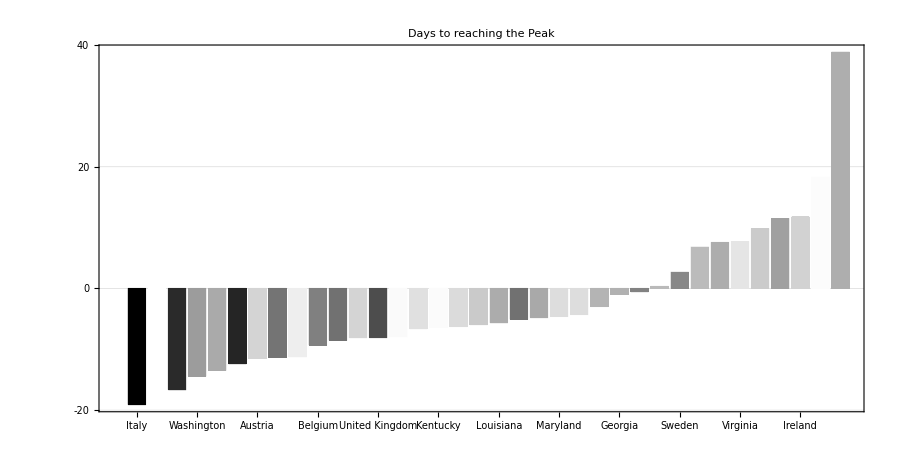

```mathematica
xx=Sort[Association[geolocate[{2,6}]/@Delete[params,25]//Rest],#1⟦1⟧<#2⟦1⟧&];
my=Min[Sqrt[(Values[xx]//Transpose)⟦2⟧]];
My=Max[Sqrt[(Values[xx]//Transpose)⟦2⟧]];
BarChart[(Values[xx]//Transpose)⟦1⟧-Last[date]⟦1⟧,ChartStyle->((GrayLevel[1-(Sqrt[#⟦2⟧]-my)/(My-my)]&/@xx)//Values),ChartLabels->{Placed[StringReplace[#["Name"],", United States"->" "]&/@Keys[xx],Axis,Rotate[#,90Degree]&]},ImageSize->900,AspectRatio->1/2,PlotLabel->"Days to reaching the Peak",PlotTheme->"Business"]
```

```mathematica
Export["~/figures/Progress.jpg",%]
```

~/figures/Progress.jpg

Displaying the skewness of the outbreak in a bar chart format:

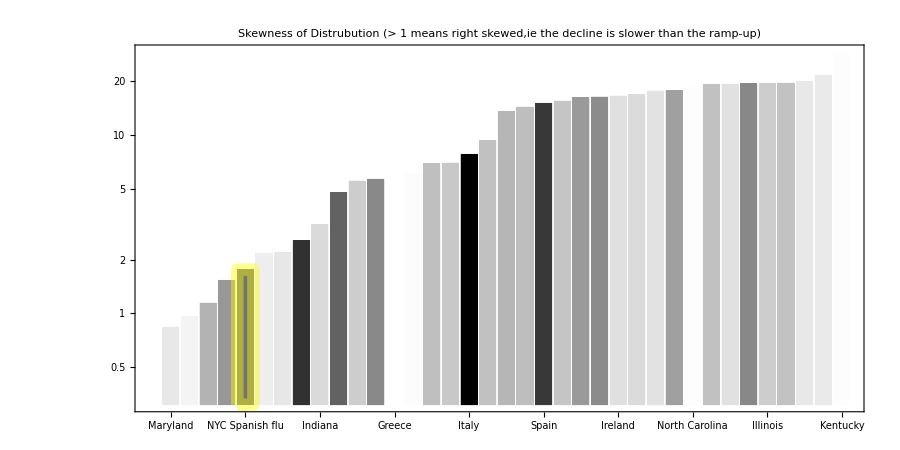

```mathematica
xx=Sort[Association[geolocate[5]/@params//Rest]];
yy=Association[geolocate[6]/@params//Rest];
my=Min[yy];
My=Max[yy];
BarChart[Values[xx],ChartStyle->(Directive[GrayLevel[1-(yy[#]-my)/(My-my)],,If[Normal[#["Population"]]==5500000,EdgeForm[{RGBColor[255/256,254/256,3/256],Thickness[0.01]}]]]&/@Keys[xx]),ChartLabels->{Placed[StringReplace[#["Name"],", United States"->" "]&/@Keys[xx],Axis,Rotate[#,90Degree]&]},ImageSize->900,AspectRatio->0.5,PlotLabel->"Skewness of Distrubution (> 1 means right skewed,ie the decline is slower than the ramp-up)",ScalingFunctions->"Log",PlotTheme->"Business"]
```

```mathematica
Export["~/figures/Skewness.jpg",%]
```

~/figures/Skewness.jpg

Displaying the speed of the outbreak in a bar char format:

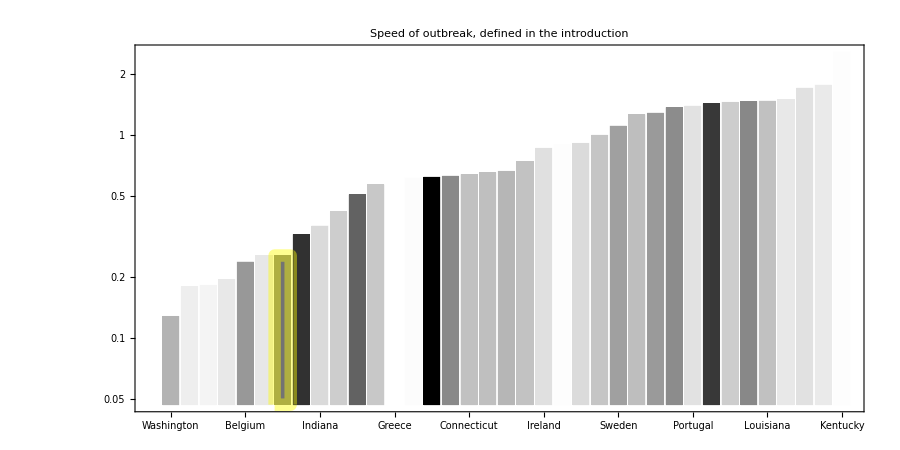

```mathematica
xx=Sort[Association[geolocate[3]/@params//Rest]];
yy=Association[geolocate[6]/@params//Rest];
my=Min[yy];
My=Max[yy];
BarChart[Values[xx],ChartStyle->(Directive[GrayLevel[1-(yy[#]-my)/(My-my)],,If[Normal[#["Population"]]==5500000,EdgeForm[{RGBColor[255/256,254/256,3/256],Thickness[0.01]}]]]&/@Keys[xx]),ChartLabels->{Placed[StringReplace[#["Name"],", United States"->" "]&/@Keys[xx],Axis,Rotate[#,90Degree]&]},ImageSize->900,AspectRatio->0.5,PlotLabel->"Speed of outbreak, defined in the introduction",ScalingFunctions->"Log",PlotTheme->"Business"]
```

```mathematica
Export["~/figures/Speed.jpg",%]
```

~/figures/Speed.jpg

Displaying the relative size of the outbreak in a bar chart format:

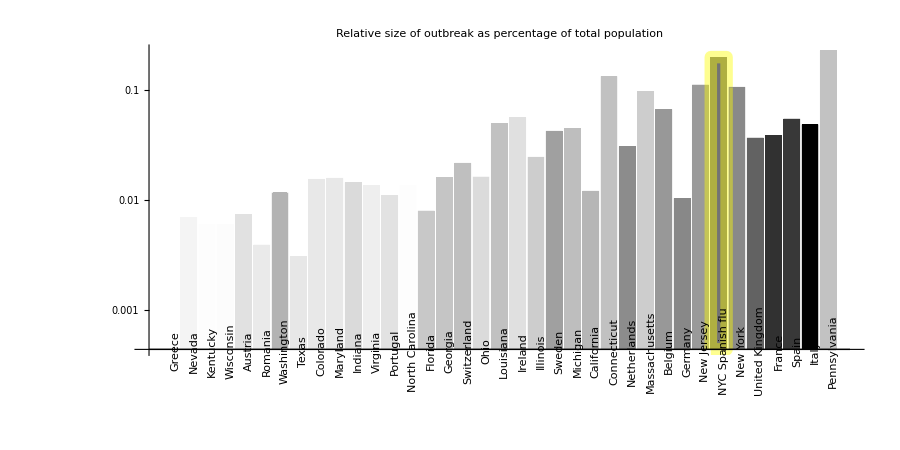

```mathematica
xx=Sort[Association[geolocate[4]/@params//Rest]];
yy=Association[geolocate[6]/@params//Rest];
my=Min[yy];
My=Max[yy];
BarChart[100*xx[#]/#["Population"]&/@Keys[xx],ChartStyle->(Directive[GrayLevel[1-(yy[#]-my)/(My-my)],If[Normal[#["Population"]]==5500000,EdgeForm[{RGBColor[255/256,254/256,3/256],Thickness[0.01]}]]]&/@Keys[xx]),ChartLabels->{Placed[StringReplace[#["Name"],", United States"->" "]&/@Keys[xx],Axis,Rotate[#,90Degree]&]},ImageSize->900,AspectRatio->0.5,PlotLabel->"Relative size of outbreak as percentage of total population",ScalingFunctions->"Log",PlotTheme->"Busines"]
```

```mathematica
Export["~/figures/Size.jpg",%]
```

~/figures/Size.jpg

## Correlating with external data

This section is still under construction. Feel free to use it and add more collateral data that you have access to and if you find something interesting, share it back with me.

```mathematica
file=Import["~/Data/AllColat.csv"];
funda=file;
parametri=file//First//Rest;
locuri=(Transpose@funda)⟦1⟧;
```

```mathematica
xx=Sort[Select[Association[geolocate[6]/@Delete[params,25]//Rest],#>250&]];
GoodRegions=xx//Keys;
```

```mathematica
temp=N@Mean@DeleteMissing[(WeatherData[airports[regionLetters[#]],"Temperature",{DatePlus[{2020,2,24},tofit[regionLetters[#]]⟦1⟧⟦1⟧-20],DatePlus[{2020,2,24},tofit[regionLetters[#]]⟦1⟧⟦1⟧+7]}]//Normal//Transpose)⟦2⟧]&;
```

```mathematica
dp=N@Mean@DeleteMissing[(WeatherData[airports[regionLetters[#]],"DewPoint",{DatePlus[{2020,2,24},tofit[regionLetters[#]]⟦1⟧⟦1⟧-20],DatePlus[{2020,2,24},tofit[regionLetters[#]]⟦1⟧⟦1⟧+7]}]//Normal//Transpose)⟦2⟧]&;
```

```mathematica
Needs["GeneralUtilities`"]
regionLetters=AssociationInvert[nowregions];
parametrize=params⟦Position[params,regionLetters[#]]⟦1⟧⟦1⟧⟧⟦{2,3,4,5}⟧/#["Population"]&;
fundamentalize=funda⟦Position[funda,regionLetters[#]]⟦1⟧⟦1⟧⟧⟦{4,5,6}⟧~Join~{temp[#],dp[#]}&;
puncte[param_,fund_]:={parametrize[#]⟦param⟧,fundamentalize[#]⟦fund⟧}&/@GoodRegions;
```

```mathematica
ListLogPlot[{fundamentalize[#]⟦5⟧,parametrize[#]⟦3⟧}&/@GoodRegions->GoodRegions,Frame->True,ImageSize->800,PlotRange->All,PlotMarkers->{Automatic,Large},GridLines->Automatic,PlotStyle->PointSize[Large]
,FrameLabel->{"Temperature","Speed of the outbreak"}]
```

-Graphics-

```mathematica
Export["~/figures/TempSpeed.jpg",%]
```

~/figures/TempSpeed.jpg

```mathematica
Correlation@@(puncte[#⟦8⟧&,4]//Transpose)
```

-0.0103797

```mathematica
speed=LinearModelFit[fundamentalize[#]~Join~{parametrize[#]⟦3⟧}&/@GoodRegions,{ρ,s,old,t,dP},{ρ,s,old,t,dP}]
```

FittedModel[-5.93896-0.84841 dP-0.0182317 old+4.95093×10^-9 s+1.25292 t-0.000228989 ρ]

```mathematica
timing=LinearModelFit[fundamentalize[#]~Join~{parametrize[#]⟦2⟧}&/@GoodRegions,{ρ,s,old,t,dP},{ρ,s,old,t,dP}]
```

FittedModel[-14.7847-10.8555 dP-0.726102 old+7.36128×10^-8 s+13.8147 t+0.00733546 ρ]

```mathematica
size=LinearModelFit[fundamentalize[#]~Join~{parametrize[#]⟦4⟧}&/@GoodRegions,{ρ,s,old,t,dP},{ρ,s,old,t,dP}]
```

FittedModel[137643.-1343.15 dP-255.491 old+0.000259121 s-16760. t+8.42414 ρ]

```mathematica
skewness=LinearModelFit[fundamentalize[#]~Join~{parametrize[#]⟦5⟧}&/@GoodRegions,{ρ,s,old,t,dP},{ρ,s,old,t,dP}]
```

FittedModel[-65.8741-10.9201 dP-0.254959 old+5.78619×10^-8 s+14.5526 t-0.00291403 ρ]

```mathematica
size["AICc"]
```

300.962

```mathematica
size["AdjustedRSquared"]
```

0.338641

```mathematica
size["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
ρ | 1 | 928832. | 928832. | 0.0145097 | 0.907506
s | 1 | 4.22593×10^8 | 4.22593×10^8 | 6.60153 | 0.0370432
old | 1 | 71696.2 | 71696.2 | 0.00112 | 0.974237
t | 1 | 1.44222×10^8 | 1.44222×10^8 | 2.25297 | 0.177049
dP | 1 | 1.86274×10^6 | 1.86274×10^6 | 0.0290988 | 0.869377
Error | 7 | 4.481×10^8 | 6.40143×10^7 |  | 
Total | 12 | 1.01778×10^9 |  |  |

```mathematica
GoodRegions//Length
```

16

```mathematica
Correlation@@Transpose[{fundamentalize[#]⟦5⟧,parametrize[#]⟦5⟧}&/@GoodRegions]
```

-0.361011